Beta Generator Algorithm

```mathematica
ClearAll["Global`*"]
```

0: a-coefficients

```mathematica
θ[t_]:=a1 Sin[t] + a3 Sin[3t] + a5 Sin[5 t]+a7 Sin[7 t];

Solve[
{
(θ[t]/.t->π/2)==b &&
(θ'[t]/.t-> 0)==2 &&
( θ''[t]/.t-> π/2)==-2γ0 /b-2b β0 &&
( θ'''[t]/.t-> 0)==c
},
{a1,a3,a5,a7}
]//FullSimplify
```

{{a1→(b (58+c+5 b (21-2 β0))-10 γ0)/(128 b),a3→(b (74+c-b (35+2 β0))-2 γ0)/(128 b),a5→(b (22-c+3 b (-7+6 β0))+18 γ0)/(384 b),a7→-(b (26+c+3 b (-5+2 β0))+6 γ0)/(384 b)}}

1: beta

```mathematica
a1[β0_,b_,c_]:=(b (58+c+5 b (21-2 β0))-10 γ0)/(128 b);
a3[β0_,b_,c_]:=(b (74+c-b (35+2 β0))-2 γ0)/(128 b);
a5[β0_,b_,c_]:=(b (22-c+3 b (-7+6 β0))+18 γ0)/(384 b);
a7[β0_,b_,c_]:=-(b (26+c+3 b (-5+2 β0))+6 γ0)/(384 b);

θ[β0_,b_,c_,t_]:= 
   a1[β0,b,c] Sin[1 t] + 
a3[β0,b,c] Sin[3t] + 
a5[β0,b,c] Sin[5 t] + 
a7[β0,b,c] Sin[7 t]

β[β0_,b_,c_,t_]:=γ0 (-1+1/4  D[θ[β0,b,c,t],t]^2)/θ[β0,b,c,t]^2-D[θ[β0,b,c,t],t,t]/(2 θ[β0,b,c,t])
```

2: maps

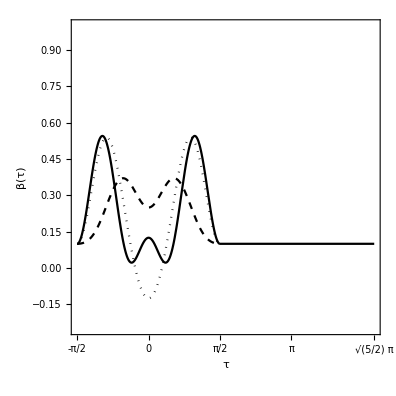

/Users/fuentes/Dropbox/betaBC.jpg

```mathematica
γ0 = 1;
b0 = 1/10;

m1 = Plot[ 
β[b0,37/20,-2,x]/.x->t ,
{t,-π/2,π/2},
PlotStyle->{Black,Dashed}
];

m2 = Plot[ 
β[b0,43/20,-1,x]/.x->t ,
{t,-π/2,π/2},
PlotStyle->{Black}
];

m3 = Plot[ 
β[b0,43/20,1,x]/.x->t ,
{t,-π/2,π/2},
PlotStyle->{Black, Dotted}
];

m4 = Plot[
b0,
{t,π/2,π/Sqrt[4 *b0]},
PlotStyle->{Black}
];

txr={-π/2,0,π/2,π,π/(2 Sqrt[1/10])};

XTicks={txr,Automatic};


maps = Show[
m1,
m2,
m3,
m4,
PlotRange->{-1/4,1},
AspectRatio->1,
Frame->True,
FrameStyle->FontSize->12,
AxesOrigin->{0,0},
FrameLabel->{"τ","β(τ)"},
FrameTicks->XTicks
]

Export[
"/Users/fuentes/Dropbox/betaBC.jpg",maps,"JPEG",
ImageResolution-> 300
]
```

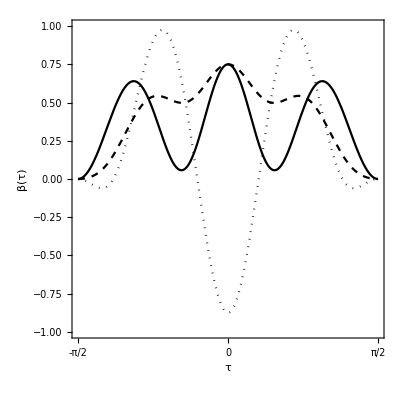

/Users/fuentes/Dropbox/betaBB.jpg

```mathematica
γ0 = Sin[t]^2;
m1 = Plot[ 
β[0,7/4,-3,x]/.x->t ,
{t,-π/2,π/2},
PlotStyle->{Black,Dashed}
];

m2 = Plot[ 
β[0,2,-3,x]/.x->t ,
{t,-π/2,π/2},
PlotStyle->{Black}
];

m3 = Plot[ 
β[0,9/5,7/2,x]/.x->t ,
{t,-π/2,π/2},
PlotStyle->{Black, Dotted}
];

txr={-π/2,0,π/2,π,3π/2 };
XTicks={txr,Automatic};

maps = Show[
m1,
m2,
m3,
PlotRange->{-1,1},
AspectRatio->1,
Frame->True,
FrameStyle->FontSize->12,
FrameLabel->{"τ","β(τ)"},
FrameTicks->XTicks
]

Export[
"/Users/fuentes/Dropbox/betaBB.jpg",maps,"JPEG",
ImageResolution-> 300
]
```

```mathematica
ClearAll["Global`*"]
```

3: beta-beta

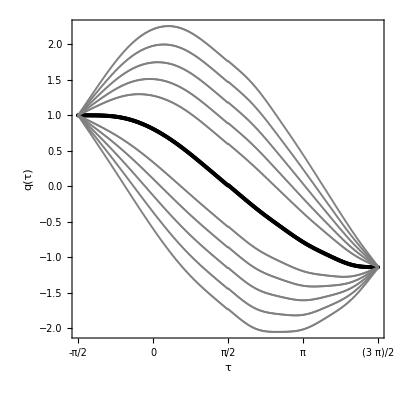

/Users/fuentes/Dropbox/qBB.jpg

```mathematica
x1 = Import["/Users/fuentes/Documents/MATLAB/x1.dat"];
x2 = Import["/Users/fuentes/Documents/MATLAB/x2.dat"];

an1 = Import["/Users/fuentes/Documents/MATLAB/an1.dat"];
bn1 = Import["/Users/fuentes/Documents/MATLAB/bn1.dat"];
cn1 = Import["/Users/fuentes/Documents/MATLAB/cn1.dat"];
dn1 = Import["/Users/fuentes/Documents/MATLAB/dn1.dat"];
en1 = Import["/Users/fuentes/Documents/MATLAB/en1.dat"];
an2 = Import["/Users/fuentes/Documents/MATLAB/an2.dat"];
bn2 = Import["/Users/fuentes/Documents/MATLAB/bn2.dat"];
cn2 = Import["/Users/fuentes/Documents/MATLAB/cn2.dat"];
dn2 = Import["/Users/fuentes/Documents/MATLAB/dn2.dat"];
en2 = Import["/Users/fuentes/Documents/MATLAB/en2.dat"];

ap1 = Import["/Users/fuentes/Documents/MATLAB/ap1.dat"];
bp1 = Import["/Users/fuentes/Documents/MATLAB/bp1.dat"];
cp1 = Import["/Users/fuentes/Documents/MATLAB/cp1.dat"];
dp1 = Import["/Users/fuentes/Documents/MATLAB/dp1.dat"];
ep1 = Import["/Users/fuentes/Documents/MATLAB/ep1.dat"];
ap2 = Import["/Users/fuentes/Documents/MATLAB/ap2.dat"];
bp2 = Import["/Users/fuentes/Documents/MATLAB/bp2.dat"];
cp2 = Import["/Users/fuentes/Documents/MATLAB/cp2.dat"];
dp2 = Import["/Users/fuentes/Documents/MATLAB/dp2.dat"];
ep2 = Import["/Users/fuentes/Documents/MATLAB/ep2.dat"];


x0 = Join[    x1[[All,1]],  x2[[All,1]]];

an = Join[  an1[[All,1]],an2[[All,1]]];
bn = Join[  bn1[[All,1]],bn2[[All,1]]];
cn = Join[  cn1[[All,1]],cn2[[All,1]]];
dn = Join[  dn1[[All,1]],dn2[[All,1]]];
en = Join[  en1[[All,1]],en2[[All,1]]];

ap = Join[  ap1[[All,1]],ap2[[All,1]]];
bp = Join[  bp1[[All,1]],bp2[[All,1]]];
cp = Join[  cp1[[All,1]],cp2[[All,1]]];
dp = Join[  dp1[[All,1]],dp2[[All,1]]];
ep = Join[  ep1[[All,1]],ep2[[All,1]]];

t0 = Array[#&,Length[x0],{-π/2,3π/2}];

q0=ListPlot[
Thread[{t0,x0}],
PlotStyle->Black
];

qx=ListPlot[
{
Thread[{t0,an}],
Thread[{t0,bn}],
Thread[{t0,cn}],
Thread[{t0,dn}],
Thread[{t0,en}],
Thread[{t0,ap}],
Thread[{t0,bp}],
Thread[{t0,cp}],
Thread[{t0,dp}],
Thread[{t0,ep}]
},
PlotStyle->Gray
];

txr={-π/2,0,π/2,π,3π/2};

XTicks={
txr,
Automatic
};

maps = Show[
q0,
qx,
PlotRange->All,
AspectRatio->1,
Frame -> True,
FrameStyle->FontSize->12,
FrameLabel->{"τ","q(τ)"},
FrameTicks->XTicks
]

Export[
"/Users/fuentes/Dropbox/qBB.jpg",maps,"JPEG",
ImageResolution-> 300
]
```

4: beta-const

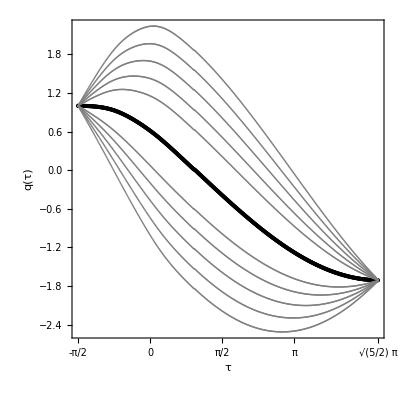

/Users/fuentes/Dropbox/qBC.jpg

```mathematica
b0 = 1/10;

x1 = Import["/Users/fuentes/Documents/MATLAB/x1.dat"];
x2 = Import["/Users/fuentes/Documents/MATLAB/x2.dat"];

an1 = Import["/Users/fuentes/Documents/MATLAB/an1.dat"];
bn1 = Import["/Users/fuentes/Documents/MATLAB/bn1.dat"];
cn1 = Import["/Users/fuentes/Documents/MATLAB/cn1.dat"];
dn1 = Import["/Users/fuentes/Documents/MATLAB/dn1.dat"];
en1 = Import["/Users/fuentes/Documents/MATLAB/en1.dat"];
an2 = Import["/Users/fuentes/Documents/MATLAB/an2.dat"];
bn2 = Import["/Users/fuentes/Documents/MATLAB/bn2.dat"];
cn2 = Import["/Users/fuentes/Documents/MATLAB/cn2.dat"];
dn2 = Import["/Users/fuentes/Documents/MATLAB/dn2.dat"];
en2 = Import["/Users/fuentes/Documents/MATLAB/en2.dat"];

ap1 = Import["/Users/fuentes/Documents/MATLAB/ap1.dat"];
bp1 = Import["/Users/fuentes/Documents/MATLAB/bp1.dat"];
cp1 = Import["/Users/fuentes/Documents/MATLAB/cp1.dat"];
dp1 = Import["/Users/fuentes/Documents/MATLAB/dp1.dat"];
ep1 = Import["/Users/fuentes/Documents/MATLAB/ep1.dat"];
ap2 = Import["/Users/fuentes/Documents/MATLAB/ap2.dat"];
bp2 = Import["/Users/fuentes/Documents/MATLAB/bp2.dat"];
cp2 = Import["/Users/fuentes/Documents/MATLAB/cp2.dat"];
dp2 = Import["/Users/fuentes/Documents/MATLAB/dp2.dat"];
ep2 = Import["/Users/fuentes/Documents/MATLAB/ep2.dat"];


x0 = Join[    x1[[All,1]],  x2[[All,1]]];

an = Join[  an1[[All,1]],an2[[All,1]]];
bn = Join[  bn1[[All,1]],bn2[[All,1]]];
cn = Join[  cn1[[All,1]],cn2[[All,1]]];
dn = Join[  dn1[[All,1]],dn2[[All,1]]];
en = Join[  en1[[All,1]],en2[[All,1]]];

ap = Join[  ap1[[All,1]],ap2[[All,1]]];
bp = Join[  bp1[[All,1]],bp2[[All,1]]];
cp = Join[  cp1[[All,1]],cp2[[All,1]]];
dp = Join[  dp1[[All,1]],dp2[[All,1]]];
ep = Join[  ep1[[All,1]],ep2[[All,1]]];

t0 = Array[#&,Length[x0],{-π/2,π/Sqrt[4 b0]}];

q0=ListPlot[
Thread[{t0,x0}],
PlotStyle->Black
];

qx=ListPlot[
{
Thread[{t0,an}],
Thread[{t0,bn}],
Thread[{t0,cn}],
Thread[{t0,dn}],
Thread[{t0,en}],
Thread[{t0,ap}],
Thread[{t0,bp}],
Thread[{t0,cp}],
Thread[{t0,dp}],
Thread[{t0,ep}]
},
PlotStyle->Gray
];

txr={-π/2,0,π/2,π,π/(2 Sqrt[1/10])};

XTicks={
txr,
Automatic
};

maps = Show[
q0,
qx,
PlotRange->All,
AspectRatio->1,
Frame -> True,
FrameStyle->FontSize->12,
FrameLabel->{"τ","q(τ)"},
FrameTicks->XTicks
]

Export[
"/Users/fuentes/Dropbox/qBC.jpg",maps,"JPEG",
ImageResolution-> 300
]
```

5: orders of magnitude

```mathematica
T=1;

c=2.99792458 10^(10);
h=1.05457266 10^(-27);
m=1.6726219×10^(-24);
e=4.8032068 10^(-10);

r= 20;

sV=299.792458;
qd=1;
pd=1;

b0=1/10;
bm=FindMaximum[β[b0,43/20,-1,t],{t,-π/2,π/2}][[1]];
t0=FindMaximum[β[b0,43/20,-1,t],{t,-π/2,π/2}][[2]];
tx=t0[[1,2]];  

q=qd Sqrt[h T/m];
p=pd Sqrt[h m/T];
v=p/m;

ϕ=(bm m r^2)/(e T^2) sV;

B=(2 √bm c m)/(e T);

σ = (2/3) e^2/(m c^3);

F= e (v/c) B;

Fosc = -(m h^2 qd)/(4 m^2 ((h T)/m)^(3/2));

Frad = m σ (3 h^3 qd)/(8 m^3 ((h T)/m)^(5/2));

EngineeringForm[ϕ]
EngineeringForm[B]
EngineeringForm[Abs[Frad/Fosc]]
```

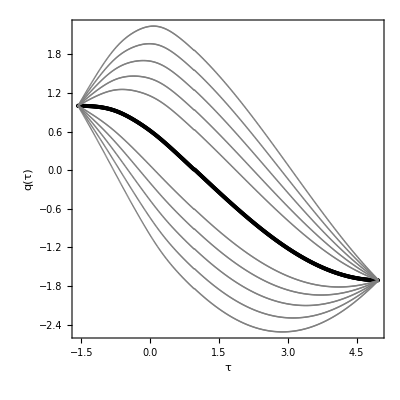

```mathematica
b0 = 1/10;

x1 = Import["/Users/fuentes/Documents/MATLAB/x1.dat"];
x2 = Import["/Users/fuentes/Documents/MATLAB/x2.dat"];

x0 = Join[    x1[[All,1]],  x2[[All,1]]];



t0 = Array[#&,Length[x0],{-π/2,π/Sqrt[4 b0]}];

q0=ListPlot[
Thread[{t0,x0}],
PlotStyle->Black
];
```